```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yinshi/Documents/work/post-doc-Humboldt/github/baryon_number_fluc/phasedata_v3/datav4

```mathematica
dataall=Table[Import["./Shi_870-960_band=15_nodes=51_more_temps/Shi_mu="<>ToString[i]<>"_m0=700.0-flag_4-51x331_VC=true.csv"],{i,870,960,5}];
```

```mathematica
n=Length[Table[i,{i,870,960,5}]]
```

19

```mathematica
dataall[[1]][[1]]
```

{T_mu,sigma,ω₀,n_B,P,e}

```mathematica
dataall[[1]][[2]]
```

{(17.0, 855.0071142042996),92.8641,0.0373279,0.00050769,0.00850413,0.425574}

```mathematica
Table[i,{i,17,50,0.1}];
```

```mathematica
Length[%]
```

331

```mathematica
pdata=Table[Table[Table[dataall[[n1]][[j*331+i]][[5]],{i,2,332}],{j,0,50}],{n1,1,19}];
```

```mathematica
Table[Table[Export["./mub"<>ToString[870+(i-1)*5]<>"/V"<>ToString[j]<>".dat",pdata[[i]][[j]]],{i,1,19}],{j,1,51}];
```

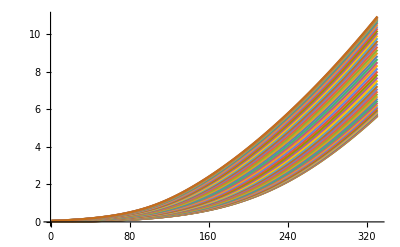

```mathematica
ListLinePlot[pdata[[1]]]
```